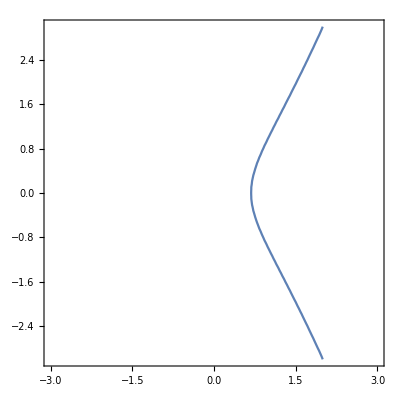

```mathematica
c1 = ContourPlot[y^2 == x^3+x-1,{x,-3,3},{y,-3,3}]
```

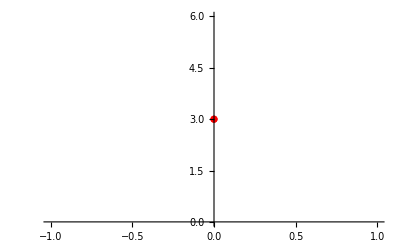

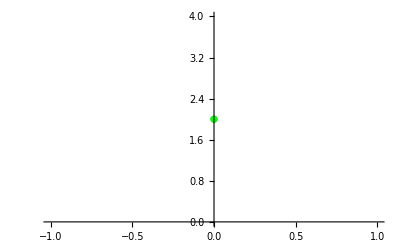

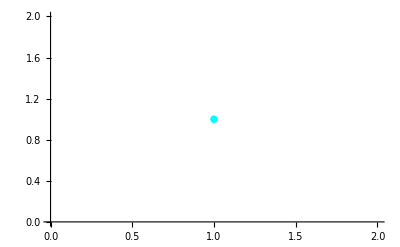

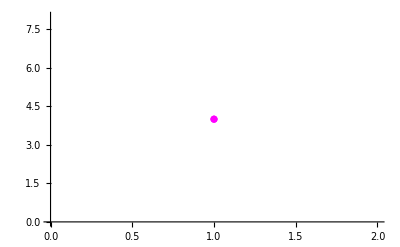

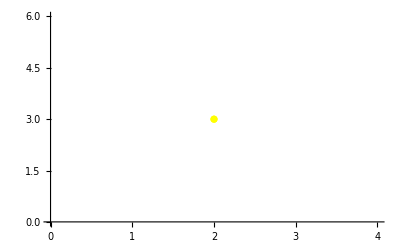

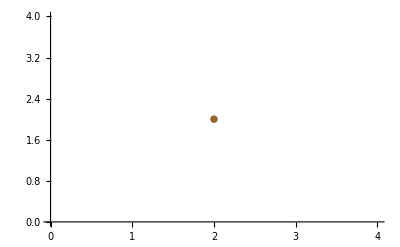

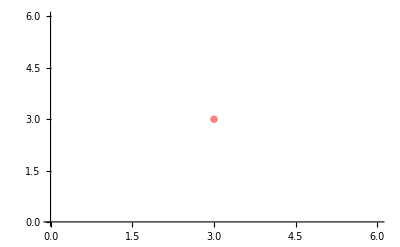

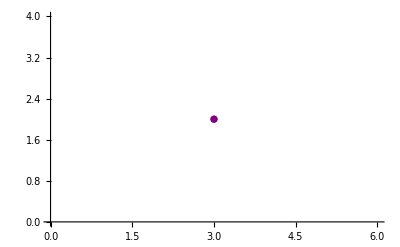

```mathematica
p1 = ListPlot[{{0,3}},PlotStyle->Red]
p2 = ListPlot[{{0,2}},PlotStyle->Green]
p3 = ListPlot[{{1,1}},PlotStyle->Cyan]
p4 = ListPlot[{{1,4}},PlotStyle->Magenta]
p5 = ListPlot[{{2,3}},PlotStyle->Yellow]
p6 = ListPlot[{{2,2}},PlotStyle->Brown]
p7 = ListPlot[{{3,3}},PlotStyle->Pink]
p8 = ListPlot[{{3,2}},PlotStyle->Purple]
```

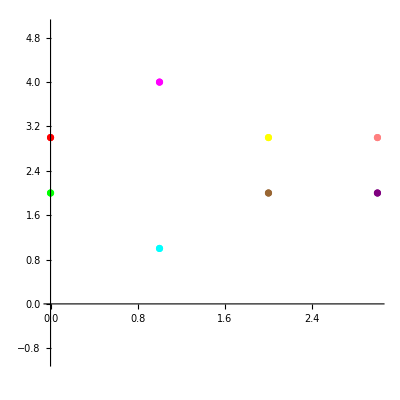

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7,p8,PlotRange->{-1,5},AspectRatio->1]
```

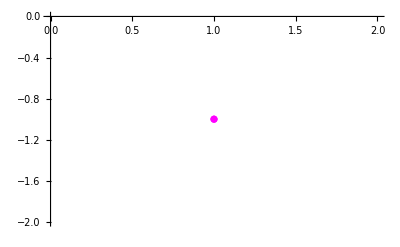

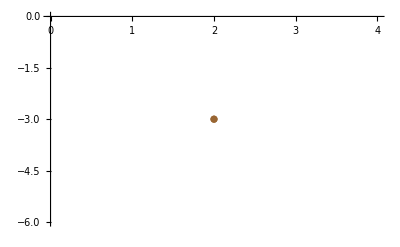

```mathematica
p4' = ListPlot[{{1,-1}},PlotStyle->Magenta]
p6' = ListPlot[{{2,-3}},PlotStyle->Brown]
```

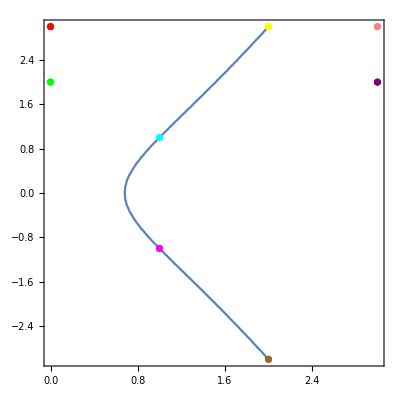

```mathematica
Show[c1,p1,p2,p3,p4',p5,p6',p7,p8,PlotRange->{-3,3},AspectRatio->1]
```